## Claswork

```mathematica
Clear[σ1,β,σ1,μ1,c,w]
σ1=1;
Integrate[ⅇ^(β*x)*1/(√(2*π)*σ1)*ⅇ^(-(x-μ1)^2/(2 σ1^2)),{x,-Infinity,Infinity}]
```

ⅇ^(1/2 β (β+2 μ1))

```mathematica
Clear[σ1]
β=-w*α*λ;
c = -w*λ*(1-α);
```

```mathematica
d=ⅇ^(μ1*β+(β^2*σ1^2)/2)*ⅇ^(μ2*c+(c^2*σ2^2)/2);
```

```mathematica
Quiet[Solve[D[d,α]==0,α]]
```

{{α→0.50625}}

## 1

```mathematica
w=400;
ξ={0,10,20,30};
p={0.25,0.25,0.25,0.25};
u[x_]:=5*x-0.01 x^2
u[100-Total[p*ξ]]
```

352.75

```mathematica
Ewminusξ=Total[p*u[w-ξ]]
```

441.5

```mathematica
sol=Solve[u[w-a]==Ewminusξ,a][[2]]
```

{a→285.462}

## 2

```mathematica
Clear[w]
```

```mathematica
u[w-a]-Total[p*u[w-ξ]]//FullSimplify
```

78.5+a (-5.-0.01 a+0.02 w)-0.3 w

```mathematica
(0.02*w+5)^2-4*0.01*(0.3*w-78.5)//Expand
```

28.14+0.188 w+0.0004 w^2

```mathematica
Solve[78.5+a*(-5-0.01*a+0.02*w)-0.3*w==0,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→-250.+w-1. √(70350.-530. w+w^2)},{a→-250.+w+√(70350.-530. w+w^2)}}

```mathematica
Solve[u[w-a]-Total[p*u[w-ξ]]==0,{a}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→-250.+w-1. √(70350.-530. w+w^2)},{a→-250.+w+√(70350.-530. w+w^2)}}

```mathematica
Total[p*u[w-ξ]]
```

0.25 (5 (-30+w)-0.01 (-30+w)^2)+0.25 (5 (-20+w)-0.01 (-20+w)^2)+0.25 (5 (-10+w)-0.01 (-10+w)^2)+0.25 (5 w-0.01 w^2)

```mathematica
Solve[D[u[x],x]==0]
```

{{x→250.}}

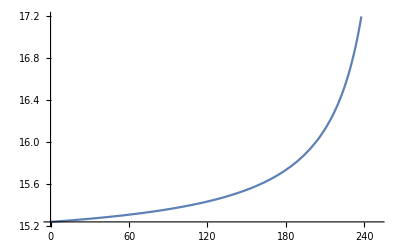

```mathematica
fun[w_]:=-250+w+√(70350-530*w+w^2)
Plot[fun[w],{w,0,250}]
```

```mathematica
Solve[D[fun[w],w]==0,w]
```

{}

```mathematica
D[fun[w],w]
```

1+(-530+2 w)/(2 √(70350-530 w+w^2))

```mathematica
u[250]
```

625.

```mathematica
fun[500]//N
```

485.266

```mathematica
Plot[u[x],{x,0,1000}]
```

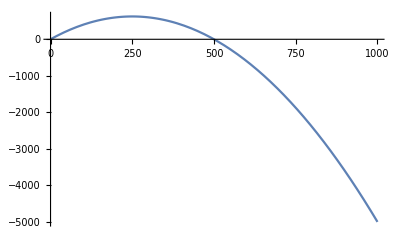

```mathematica
Solve[
```

```mathematica
Limit[-250+w-√(70350-530*w+w^2),w->-Infinity]
```

-∞

```mathematica
fun[1000000]//N
```

1.99949×10^6

## 3

```mathematica
w=100;
u[x_]:=Log[x]
```

```mathematica
log10 = Integrate[Log10[100-x]*√(25-x^2),{x,0,5}]//N
```

39.0862

```mathematica
log =Integrate[Log[100-x]*√(25-x^2),{x,0,5}]//N
```

89.9994

```mathematica
D[Log[100-x],x]
```

-1/(100-x)

```mathematica
Integrate[√(25-x^2),x]
```

1/2 x √(25-x^2)+25/2 ArcSin[x/5]

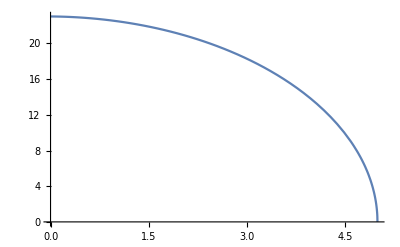

```mathematica
Plot[Log[100-x]*√(25-x^2),{x,0,5}]
```

```mathematica
Solve[Log10[100-a]==log10*a,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→0.0511632}}

```mathematica
Solve[Log[100-a]==log*a,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→0.0511632}}

## 4

```mathematica
β=-w*α*λ;
d=ⅇ^(μ1*β+(β^2*σ1^2)/2)
```

ⅇ^(-w α λ μ1+1/2 w^2 α^2 λ^2 σ1^2)

```mathematica
Solve[D[ⅇ^(r1*λ*w*α)*d,α]==0,α]
```

{{α→(-r1+μ1)/(w λ σ1^2)}}

## 5

```mathematica
Clear[σ1,β,σ1,μ1,c,w]
Clear[σ1]
β=-w*α*λ;
c = -w*λ*(1-α);
d=ⅇ^(μ1*β+(β^2*σ1^2)/2)
```

ⅇ^(-w α λ μ1+1/2 w^2 α^2 λ^2 σ1^2)

```mathematica
Solve[D[d,α]==0,α]
```

{{α→μ1/(w λ σ1^2)}}

```mathematica
D[d,α]==0
```

ⅇ^(-w α λ μ1+1/2 w^2 α^2 λ^2 σ1^2) (-w λ μ1+w^2 α λ^2 σ1^2)==0

```mathematica
Clear[σ1,c]
β=-w*α*λ;
c = -w*λ*(1-α);
```

```mathematica
d=ⅇ^(μ1*β+(β^2*σ1^2)/2)*ⅇ^(μ2*c+(c^2*σ2^2)/2)
```

ⅇ^(-w α λ μ1-w (1-α) λ μ2+1/2 w^2 α^2 λ^2 σ1^2+1/2 w^2 (1-α)^2 λ^2 σ2^2)

```mathematica
solr=Clear[σ1,β,σ1,μ1,c,w]
Integrate[(ⅇ^(β*x))^2*1/(√(2*π)*σ1)*ⅇ^(-(x-μ1)^2/(2 σ1^2)),{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(2 β (μ1+β σ1^2)))/(√(1/σ1^2) σ1),Re[σ1^2]>0]

```mathematica
Clear[w,λ,μ1,μ2,σ1,σ2,ρ]
β=-w*α*λ;
e1=ⅇ^(μ1*β+(β^2*σ1^2)/2);
d1=ⅇ^(2 β (μ1+β σ1^2))-e1^2;
```

```mathematica
c = -w*λ*(1-α);
e2=ⅇ^(μ2*c+(c^2*σ2^2)/2);
d2=ⅇ^(2 c (μ1+c σ1^2))-e2^2;
```

```mathematica
w=100;
λ=0.2;
μ1=5;
μ2=4;
σ1=2;
σ2=2;
ρ=0.5;
```

```mathematica
cer = ρ*√(d1*d2)+e1*e2//FullSimplify
```

4.92070093026438×10^312 ⅇ^(α (-1620.+1600. α))

```mathematica
Solve[D[cer,α]==0,α]
```

{{α→0.50625}}